# Diagnostic Performance vs Latent Dimension

## Parameters regression

This notebook summarizes diagonal-test performance for ENCA models trained with different latent-space dimensions. For each z dimension, the diagnostic output provides the Pearson correlation and normalized RMSE for each physical parameter. The plots compare correlation with a baseline-corrected performance score, using the prior-mean predictor as the zero-performance reference.

The numerical pairs below are copied from the output of diag_test.py. For each parameter and latent dimension, the first number is the Pearson correlation between true and predicted parameter values, and the second number is RMSE divided by the prior range, reported in percent.

```mathematica
τ5={0.9353,10.8};
T5={0.9510,9.3};
Nd5={0.9121,13.1};
σ5={0.9146,11.8};
Bmax5={0.9733,7.8};
```

```mathematica
τ6={0.9776,6.1};
T6={0.8528,15.4};
Nd6={0.4464,26.0};
σ6={0.0035,29.3};
Bmax6={0.9367,10.0};
```

```mathematica
τ7={0.9816,5.5};
T7={0.9780,6.2};
Nd7={0.9611,7.9};
σ7={0.9099,12.1};
Bmax7={0.9822,5.7};
```

```mathematica
τ8={0.9826,5.4};
T8={0.9658,7.7};
Nd8={0.8997,12.5};
σ8={0.0195,29.2};
Bmax8={0.9668,7.3};
```

```mathematica
τ9={0.9911,3.8};
T9={0.9869,4.8};
Nd9={0.9635,7.7};
σ9={-0.0095,29.3};
Bmax9={0.9872,4.6};
```

```mathematica
τ10={0.9847,5.0};
T10={0.9861,4.9};
Nd10={0.9393,10.0};
σ10={-0.0034,29.4};
Bmax10={0.9869,4.6};
```

```mathematica
τ11={0.9883,4.4};
T11={0.9873,4.7};
Nd11={0.9535,8.8};
σ11={0.0413,29.2};
Bmax11={0.9876,4.5};
```

```mathematica
τ12={0.9914,3.8};
T12={0.9888,4.4};
Nd12={0.9507,9.1};
σ12={0.0277,29.2};
Bmax12={0.9894,4.2};
```

```mathematica
τ13={0.9872,4.6};
T13={0.9862,4.9};
Nd13={0.9347,10.2};
σ13={-0.0295,29.4};
Bmax13={0.9903,4.0};
```

```mathematica
τ14={0.9926,3.5};
T14={0.9924,3.6};
Nd14={0.9644,7.7};
σ14={-0.0433,29.4};
Bmax14={0.9916,3.7};
```

```mathematica
τ15={0.9928,3.4};
T15={0.9926,3.6};
Nd15={0.9711,6.8};
σ15={0.0031,29.3};
Bmax15={0.9911,3.8};
```

```mathematica
τ16={0.9867,4.7};
T16={0.9861,4.9};
Nd16={0.9618,7.9};
σ16={0.0136,29.3};
Bmax16={0.9874,4.6};
```

```mathematica
zDims={5,6,7,8,9,10,11,12,13,14,15,16};
```

```mathematica
paramData=<|"τ"->{τ5,τ6,τ7,τ8,τ9,τ10,τ11,τ12,τ13,τ14,τ15,τ16},"T"->{T5,T6,T7,T8,T9,T10,T11,T12,T13,T14,T15,T16},"Nd"->{Nd5,Nd6,Nd7,Nd8,Nd9,Nd10,Nd11,Nd12,Nd13,Nd14,Nd15,Nd16},"σ"->{σ5,σ6,σ7,σ8,σ9,σ10,σ11,σ12,σ13,σ14,σ15,σ16},"Bmax"->{Bmax5,Bmax6,Bmax7,Bmax8,Bmax9,Bmax10,Bmax11,Bmax12,Bmax13,Bmax14,Bmax15,Bmax16}|>
```

<|τ→{{0.9353,10.8},{0.9776,6.1},{0.9816,5.5},{0.9826,5.4},{0.9911,3.8},{0.9847,5.},{0.9883,4.4},{0.9914,3.8},{0.9872,4.6},{0.9926,3.5},{0.9928,3.4},{0.9867,4.7}},T→{{0.951,9.3},{0.8528,15.4},{0.978,6.2},{0.9658,7.7},{0.9869,4.8},{0.9861,4.9},{0.9873,4.7},{0.9888,4.4},{0.9862,4.9},{0.9924,3.6},{0.9926,3.6},{0.9861,4.9}},Nd→{{0.9121,13.1},{0.4464,26.},{0.9611,7.9},{0.8997,12.5},{0.9635,7.7},{0.9393,10.},{0.9535,8.8},{0.9507,9.1},{0.9347,10.2},{0.9644,7.7},{0.9711,6.8},{0.9618,7.9}},σ→{{0.9146,11.8},{0.0035,29.3},{0.9099,12.1},{0.0195,29.2},{-0.0095,29.3},{-0.0034,29.4},{0.0413,29.2},{0.0277,29.2},{-0.0295,29.4},{-0.0433,29.4},{0.0031,29.3},{0.0136,29.3}},Bmax→{{0.9733,7.8},{0.9367,10.},{0.9822,5.7},{0.9668,7.3},{0.9872,4.6},{0.9869,4.6},{0.9876,4.5},{0.9894,4.2},{0.9903,4.},{0.9916,3.7},{0.9911,3.8},{0.9874,4.6}}|>

```mathematica
corr[param_]:=paramData[param][[All,1]];

baselineError=1/Sqrt[12];
perf[param_]:=1-(paramData[param][[All,2]]/100)/baselineError;
```

Performance score 
For each physical parameter, the diagnostic test reports 
normalized RMSE=RMSE/prior range.
Since the parameters are sampled uniformly from their prior intervals, a trivial baseline predictor is one that always predicts the prior mean, i.e. the midpoint of the allowed interval.
For a uniform distribution on[a,b], the standard deviation is (b-a)/Sqrt[12].
Therefore,the normalized RMSE of this trivial mean predictor is 
baselineError=((b-a)/Sqrt[12])/(b-a)=1/Sqrt[12].
We define the baseline-corrected performance score as 
performance=1-normalizedRMSE/baselineError=1-(RMSE/prior range)/(1/Sqrt[12]).

Interpretation:
performance=1  --- perfect prediction,RMSE=0 
performance=0  --- no better than always predicting the prior mean 
performance<0 ---  worse than the prior-mean predictor 

Thus this score measures the fraction of the naive baseline error removed by the encoder.
For example, performance=0.6 means that the model has reduced the RMSE by about 60% relative to always predicting the prior mean.

```mathematica
dualAxisPlot[title_,corrVals_,perfVals_]:=Module[{perfData,corrData},
perfData=Transpose[{zDims,perfVals}];
corrData=Transpose[{zDims,corrVals}];
ListLinePlot[{perfData,corrData},
Frame->True,Axes->False,
PlotMarkers->{Automatic,16},
PlotStyle->{Blue,Darker[Red]},PlotLegends->Placed[{"1 - (mean) normalized RMSE","mean corr"},Above],FrameLabel->{"latent dimension z","performance score",None,"correlation"},FrameTicks->{{Automatic,Automatic},{Thread[{zDims,zDims}],None}},PlotRange->{{Min[zDims]-1,Max[zDims]+1},{-0.05,1.02}},GridLines->{zDims,Automatic},
ImageSize->520,
PlotLabel->title]]
```

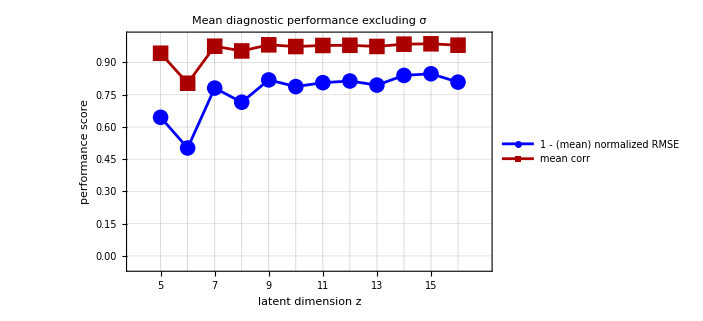

```mathematica
paramsNoSigma={"τ","T","Nd","Bmax"};

meanCorrNoSigma=Mean/@Transpose[corr/@paramsNoSigma];
meanPerfNoSigma=Mean/@Transpose[perf/@paramsNoSigma];

dualAxisPlot["Mean diagnostic performance excluding σ",meanCorrNoSigma,meanPerfNoSigma]
```

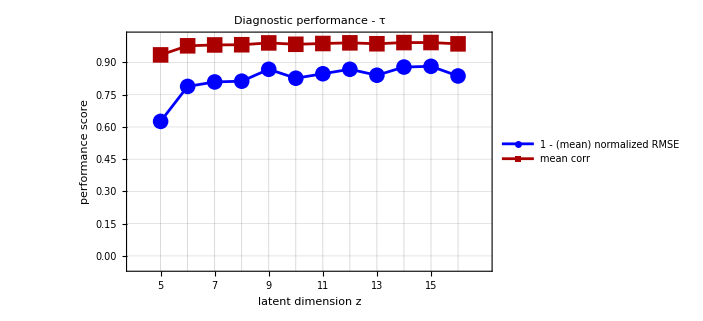

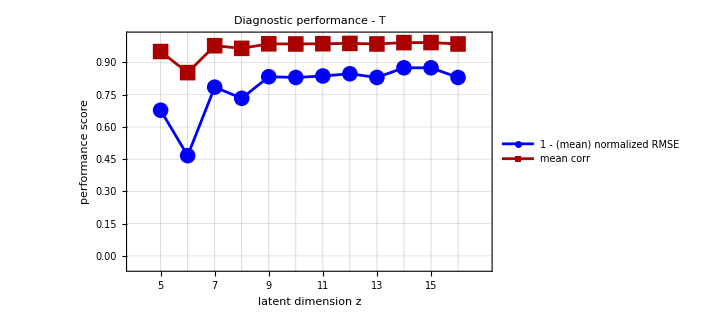

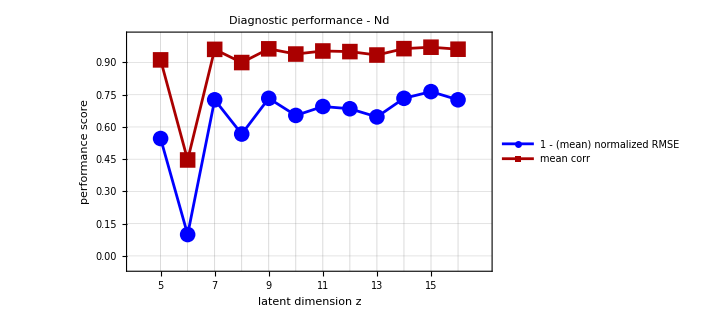

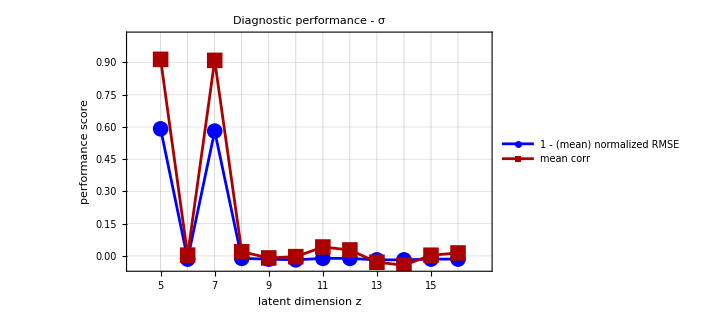

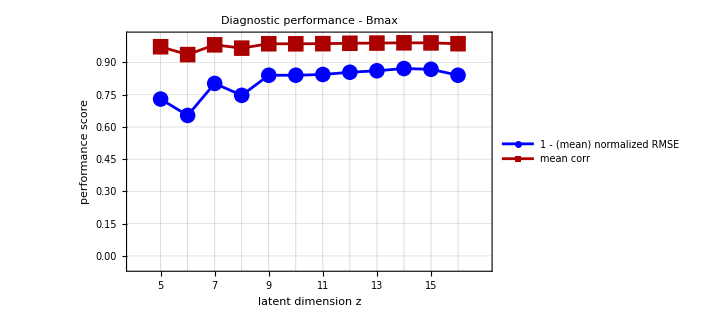

```mathematica
dualAxisPlot["Diagnostic performance - τ",corr["τ"],perf["τ"]]
dualAxisPlot["Diagnostic performance - T",corr["T"],perf["T"]]
dualAxisPlot["Diagnostic performance - Nd",corr["Nd"],perf["Nd"]]
dualAxisPlot["Diagnostic performance - σ",corr["σ"],perf["σ"]]
dualAxisPlot["Diagnostic performance - Bmax",corr["Bmax"],perf["Bmax"]]
```

## Reconstruction

Parameters : tau = 5, T = 6, Nd = 12, sigma = 0.02, Bmax = 8
nseeds = 10

Reconstruction performance
The reconstruction tests are run with the same physical parameters and the same number of noise realizations for each latent dimension, so the reported mean_RMSE values from recon_test.py are directly comparable. Lower mean_RMSE means better reconstruction.

To plot a higher-is-better score, the RMSE values are normalized by the worst RMSE among the currently tested latent dimensions:

reconstruction performance = 1 - meanRMSE/rmseRef,

where rmseRef = Max[meanRMSE]. With this definition, performance = 1 would correspond to perfect reconstruction, while performance = 0 corresponds to the worst model in the current comparison set. For example, a value of 0.47 means that the model reduces the reconstruction RMSE by about 47% relative to the current worst model.

```mathematica
zdim={5,6,7,8,9,10,11,12,13,14,15,16};
meanRMSE={111.62,84.7185,126.544,45.0629,41.4998,51.158,49.7209,40.5403,53.6159,35.1991,36.1268,33.6647};
```

```mathematica
rmseRef=Max[meanRMSE];
reconPerf=1-meanRMSE/rmseRef;
```

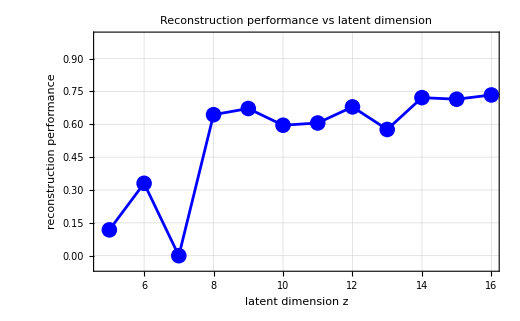

```mathematica
ListLinePlot[Transpose[{zdim,reconPerf}],Frame->True,Axes->False,PlotMarkers->{Automatic,16},PlotStyle->Blue,FrameLabel->{"latent dimension z","reconstruction performance"},PlotLabel->"Reconstruction performance vs latent dimension",GridLines->Automatic,PlotRange->{-0.05,1},ImageSize->520]
```